```mathematica
f[x_]:=(1-(x^2-xmu2)/((x x-xmu2)^2+xdt2)^(1/2))x x
```

```mathematica
f[x]
```

x^2 (1-(x^2-xmu2)/(√(xdt2+(x^2-xmu2)^2)))

```mathematica
NIntegrate[f[x]/.{xmu2->1,xdt2->0.0001},{x,0,Infinity}]
```

0.666846

```mathematica
N[%]
```

0.666846

```mathematica
NSolve[NIntegrate[(f[x]/.{xmu2->0.9}),{x,0,Infinity}]==2/3,{xdt2},Reals]
```

NIntegrate::inumr: The integrand x^2\ (1 - -0.9 + x^2/√(-0.9 + Power[« 2 »])^2 + xdt2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

{}

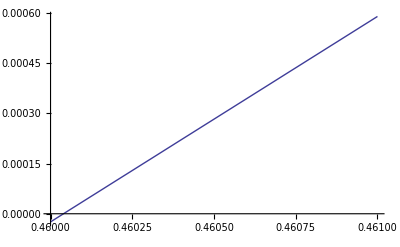

```mathematica
Plot[NIntegrate[(f[x]/.{xmu2->0.6}),{x,0,Infinity}]-2/3,{xdt2,0.46,0.461}]
```

```mathematica
N[8Pi^3/3]
```

82.6834

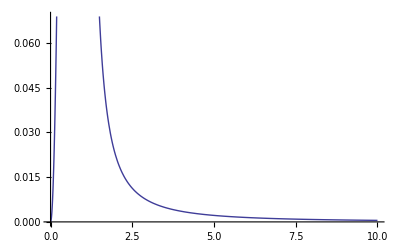

```mathematica
Plot[f[x]/.{xmu2->0.99,xdt2->0.1},{x,0,10}]
```

```mathematica
muDtL={{0.999,0.00064},{0.99,0.0079665},{0.95,0.059435},{0.93,0.0693},{0.9,0.10298},{0.7,0.34},{0.6,0.46005},{0.5,.577},{.3,.8005},{.1,1.01},{0,1.107},{-0.1,1.2},{-0.3,1.38},{-.5,1.545},{-.7,1.7},{-.9,1.854},{-1,1.915},{-1.5,2.24},{-2,2.525},{-2.5,2.785},{-3,3.02},{-4,3.46},{-5,3.85},{-6,4.2},{-8,4.85},{-10,5.4}}
```

{{0.999,0.00064},{0.99,0.0079665},{0.95,0.059435},{0.93,0.0693},{0.9,0.10298},{0.7,0.34},{0.6,0.46005},{0.5,0.577},{0.3,0.8005},{0.1,1.01},{0,1.107},{-0.1,1.2},{-0.3,1.38},{-0.5,1.545},{-0.7,1.7},{-0.9,1.854},{-1,1.915},{-1.5,2.24},{-2,2.525},{-2.5,2.785},{-3,3.02},{-4,3.46},{-5,3.85},{-6,4.2},{-8,4.85},{-10,5.4}}

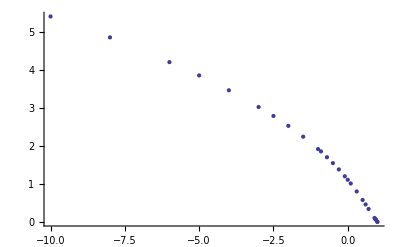

```mathematica
ListPlot[muDtL]
```

```mathematica
f1[x_]:=(x x)/((x x-xmu2)^2+xdt4)^(1/2)-1
```

```mathematica
f1[x]
```

-1+x^2/(√(xdt4+(x^2-xmu2)^2))

```mathematica
f1[x]mu{xmu2->1,xdt4->2}
```

{mu (-1+x^2/(√(xdt4+(x^2-xmu2)^2))) (xmu2→1),mu (-1+x^2/(√(xdt4+(x^2-xmu2)^2))) (xdt4→2)}

```mathematica
length=Length[muDtL];intact={};
For[i=1,i≤length,i++,
strength=2/Pi NIntegrate[f1[x]/.{xmu2->muDtL[[i,1]],xdt4->muDtL[[i,2]]},{x,0,Infinity}];intact=Append[intact,strength]]
```

```mathematica
intact
```

{2.38973,1.5756,0.899421,0.830708,0.680721,0.166638,0.0128024,-0.113235,-0.316811,-0.481182,-0.553235,-0.620286,-0.742788,-0.852479,-0.952547,-1.04524,-1.08865,-1.28824,-1.46346,-1.6213,-1.76587,-2.02578,-2.25686,-2.46689,-2.84159,-3.17282}

```mathematica
muL=Transpose[muDtL][[1]];dtL=Transpose[muDtL][[2]]^(1/2);
```

```mathematica
muL
```

{0.999,0.99,0.95,0.93,0.9,0.7,0.6,0.5,0.3,0.1,0,-0.1,-0.3,-0.5,-0.7,-0.9,-1,-1.5,-2,-2.5,-3,-4,-5,-6,-8,-10}

```mathematica
Transpose[{intact,muL}]
```

{{2.38973,0.999},{1.5756,0.99},{0.899421,0.95},{0.830708,0.93},{0.680721,0.9},{0.166638,0.7},{0.0128024,0.6},{-0.113235,0.5},{-0.316811,0.3},{-0.481182,0.1},{-0.553235,0},{-0.620286,-0.1},{-0.742788,-0.3},{-0.852479,-0.5},{-0.952547,-0.7},{-1.04524,-0.9},{-1.08865,-1},{-1.28824,-1.5},{-1.46346,-2},{-1.6213,-2.5},{-1.76587,-3},{-2.02578,-4},{-2.25686,-5},{-2.46689,-6},{-2.84159,-8},{-3.17282,-10}}

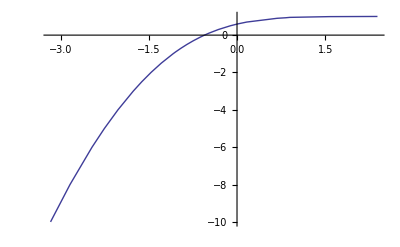

```mathematica
muPlot=ListLinePlot[Transpose[{intact, muL}]]
```

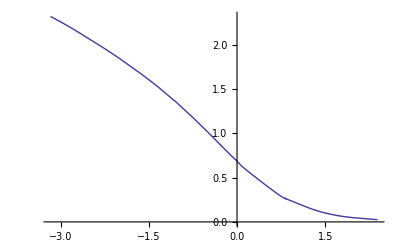

```mathematica
dtPlot=ListLinePlot[Transpose[{intact,dtL}],InterpolationOrder->2]
```

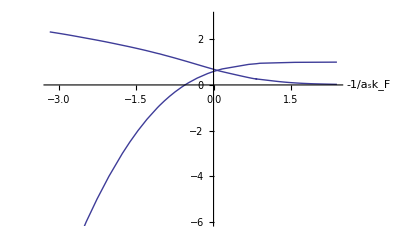

```mathematica
Show[dtPlot,muPlot,AxesLabel->{"-1/a_sk_F",""},AxesOrigin->{0,0},LabelStyle->Directive[Bold,Larger], PlotRange->{-6,3}]
```

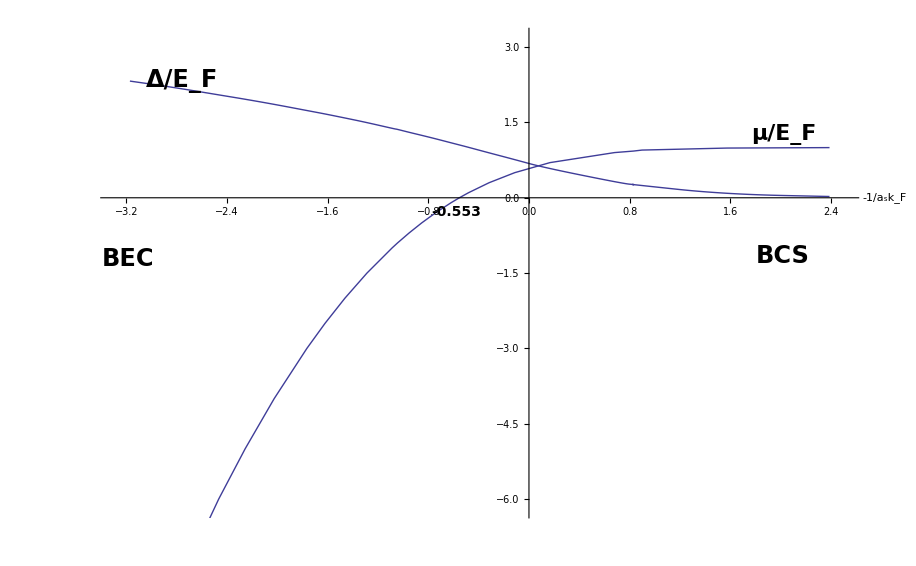

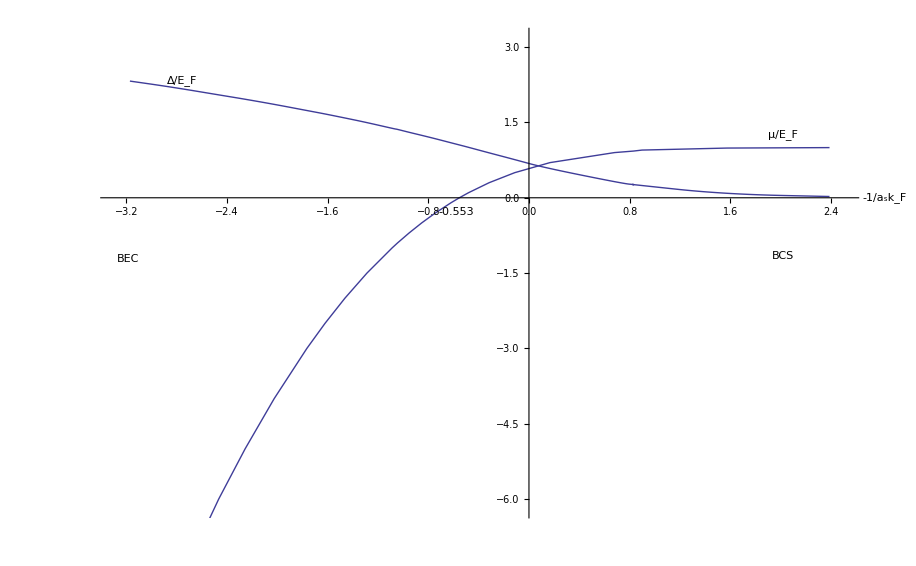

```mathematica
alpha2=3*2^(1/2)*dtL^2/(128*(dtt *2)^(1/2))
```

{0.000015/(√dtt),0.000186715/(√dtt),0.00139301/(√dtt),0.00162422/(√dtt),0.00241359/(√dtt),0.00796875/(√dtt),0.0107824/(√dtt),0.0135234/(√dtt),0.0187617/(√dtt),0.0236719/(√dtt),0.0259453/(√dtt),0.028125/(√dtt),0.0323438/(√dtt),0.0362109/(√dtt),0.0398438/(√dtt),0.0434531/(√dtt),0.0448828/(√dtt),0.0525/(√dtt),0.0591797/(√dtt),0.0652734/(√dtt),0.0707813/(√dtt),0.0810938/(√dtt),0.0902344/(√dtt),0.0984375/(√dtt),0.113672/(√dtt),0.126563/(√dtt)}

```mathematica
weight=1/(1+alpha2)^(2/3);shiftIntact=intact*(2weight)^(1/2)+muL*2;intactShift=(shiftIntact*weight);
```

```mathematica
intactSt2=intact*(2*30)^(1/2)+muL*2
```

{20.5087,14.1845,8.86689,8.29464,7.07284,2.69077,1.29917,0.122885,-1.85401,-3.52722,-4.28534,-5.00472,-6.35361,-7.60327,-8.7784,-9.89641,-10.4326,-12.9787,-15.3359,-17.5585,-19.6784,-23.6916,-27.4816,-31.1084,-38.0109,-44.5765}

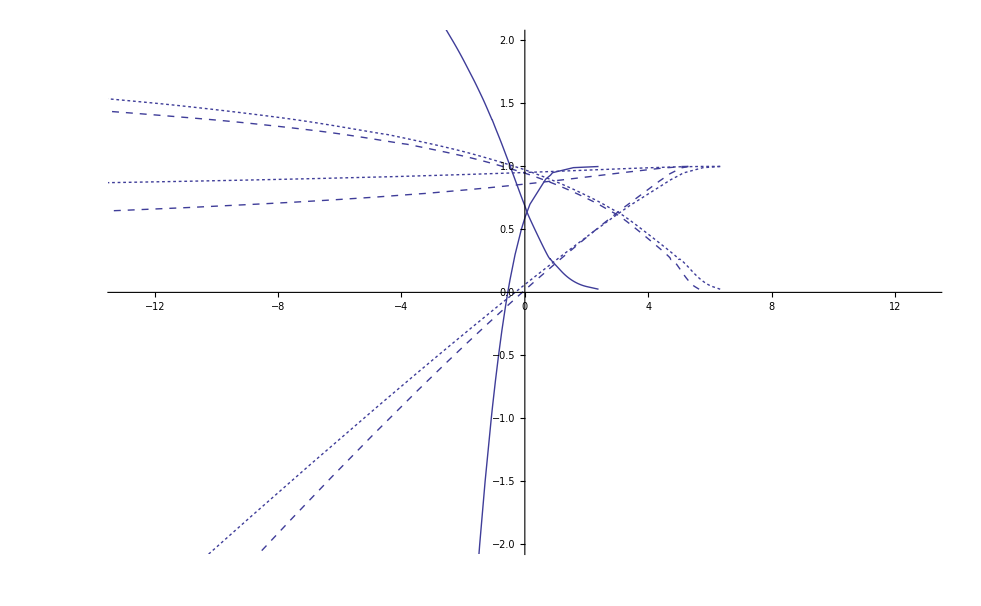

```mathematica
muPlotSt=ListLinePlot[Transpose[{intactShift,muL*weight}]/.{dtt->0.01},PlotStyle->{Dashed}];
wPlot=ListLinePlot[Transpose[{intactShift,weight}]/.{dtt->.01},PlotStyle->{Dashed}];
dtPlotSt=ListLinePlot[Transpose[{intactShift,dtL*weight}]/.{dtt->.03},InterpolationOrder->2,PlotStyle->{Dashed}];
muPlotSt2=ListLinePlot[Transpose[{intactShift, muL*weight}]/.{dtt->0.1},PlotStyle->{Dashing[Tiny]}];dtPlotSt2=ListLinePlot[Transpose[{intactShift,dtL*weight}]/.{dtt->0.1},InterpolationOrder->2,PlotStyle->{Dashing[Tiny]}];
wPlotSt2=ListLinePlot[Transpose[{intactShift,weight}]/.{dtt->.1},PlotStyle->{Dashing[Tiny]}];
Show[dtPlotSt,muPlotSt,dtPlot,wPlot,muPlot,muPlotSt2,dtPlotSt2,wPlotSt2,AxesOrigin->{0,0},LabelStyle->Directive[Bold,Larger], PlotRange->{{-13,13},{-2,2}}]
```

```mathematica
ListLinePlot[Transpose[{intactShift, muL*weight}]/.{dtt->0.1.08}]
```

-Graphics-

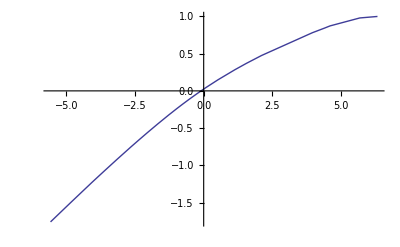

```mathematica
ListLinePlot[Transpose[{intactShift,muL*weight}]/.{dtt->0.1}]
```

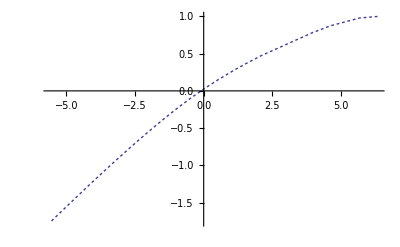

```mathematica
ListLinePlot[Transpose[{intactShift, muL*weight}]/.{dtt->0.1},PlotStyle->{Dashing[Tiny]}]
```

```mathematica
muPlotSt3=ListLinePlot[Transpose[{intactShift,muL*weight}]/.{dtt->0.001}];
wPlot3=ListLinePlot[Transpose[{intactShift,weight^(3/2)}]/.{dtt->.001}];
dtPlotSt3=ListLinePlot[Transpose[{intactShift,dtL*weight}]/.{dtt->.001},InterpolationOrder->2];
```

```mathematica
Show[dtPlotSt3,muPlotSt3,wPlot3,AxesOrigin->{0,0},LabelStyle->Directive[Bold,Larger], PlotRange->{{-10,5},{-2,1.5}}]
```

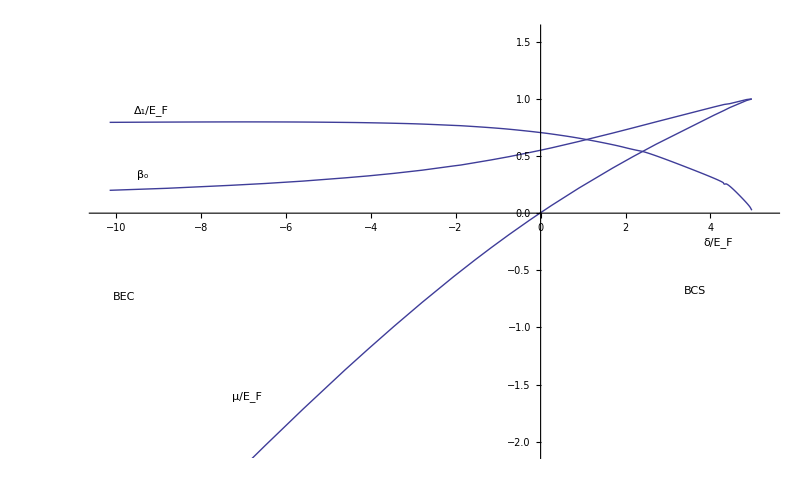

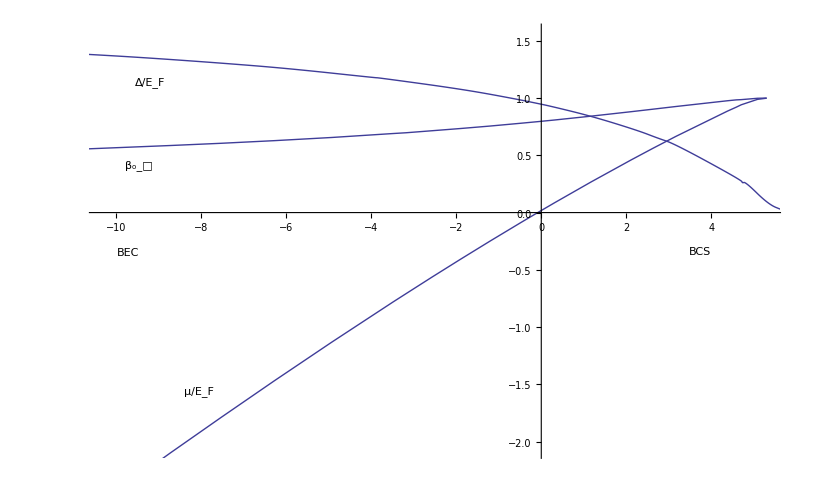

-Graphics-

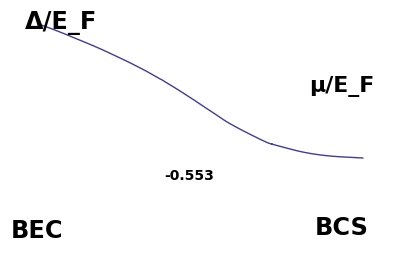
```mathematica
s=-Graphics-
```

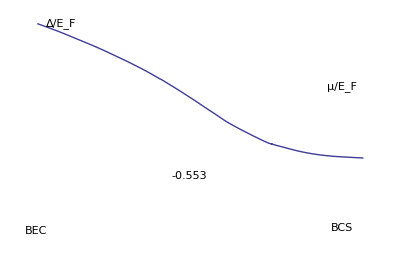

```mathematica
muDtL[[1]]
```

{0.999,0.00064}

```mathematica
Length[muDtL]
```

26

```mathematica
a=0;a=
```

ListLinePlot::ioproc: {{1.998  + 3.37958\ √dtt, 0.0252982}, {1.98  + 2.22823\ √dtt, 0.0892553}, {1.9  + 1.27197\ √dtt, 0.243793}, {1.86  + 1.1748\ √dtt, 0.263249}, {1.8  + 0.962685\ √dtt, 0.320905}, « 16 », {-8 - 2.86488\ √dtt, 1.86011}, {-10 - 3.19168\ √dtt, 1.96214}, {-12 - 3.4887\ √dtt, 2.04939}, {-16 - 4.01862\ √dtt, 2.20227}, {-20 - 4.48704\ √dtt, 2.32379}}
 may contain non-machine precision numbers, complex numbers, or invalid entries.

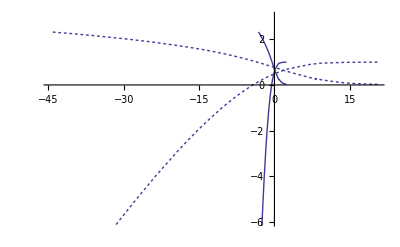

```mathematica
muPlotSt=ListLinePlot[Transpose[{shiftIntact, muL}],PlotStyle->{Dashed}];dtPlotSt=ListLinePlot[Transpose[{shiftIntact,dtL}],InterpolationOrder->2,PlotStyle->{Dashed}];
muPlotSt2=ListLinePlot[Transpose[{intactSt2, muL}],PlotStyle->{Dashing[Tiny]}];dtPlotSt2=ListLinePlot[Transpose[{intactSt2,dtL}],InterpolationOrder->2,PlotStyle->{Dashing[Tiny]}];
Show[dtPlotSt,muPlotSt,dtPlot,muPlot,muPlotSt2,dtPlotSt2,AxesOrigin->{0,0},LabelStyle->Directive[Bold,Larger], PlotRange->{-6,3}]
```

```mathematica
Transpose[{intactShift,weight}]/.{dtt->0.1}
```

{{3.06669,0.99999},{2.6843,0.999876},{2.30011,0.999078},{2.22911,0.998925},{2.10107,0.998404},{1.46679,0.994755},{1.19719,0.992919},{0.940948,0.991139},{0.452708,0.98776},{-0.0149574,0.984618},{-0.243251,0.983171},{-0.468707,0.98179},{-0.912729,0.979129},{-1.34907,0.976706},{-1.77933,0.974443},{-2.20443,0.972208},{-2.41555,0.971327},{-3.4569,0.966662},{-4.48048,0.962618},{-5.49013,0.958964},{-6.48888,0.955692},{-8.45745,0.94964},{-10.3967,0.944355},{-12.3128,0.939674},{-16.0814,0.931133},{-19.7923,0.924055}}

```mathematica
weight/.{dtt->0.001}
```

{0.999901,0.998765,0.990876,0.989382,0.984322,0.95046,0.934388,0.919369,0.892276,0.868619,0.858186,0.848473,0.83043,0.814709,0.800601,0.787173,0.782008,0.755854,0.734642,0.71654,0.701106,0.674323,0.652618,0.634563,0.604121,0.581047}

```mathematica
weight
```

{1/((1+(4.71405×10^-6)/(√dtt))^(2/3)),1/(1+0.0000586788/(√dtt))^(2/3),1/(1+0.00043778/(√dtt))^(2/3),1/(1+0.000510443/(√dtt))^(2/3),1/(1+0.000758519/(√dtt))^(2/3),1/(1+0.00250434/(√dtt))^(2/3),1/(1+0.00338859/(√dtt))^(2/3),1/(1+0.00425001/(√dtt))^(2/3),1/(1+0.00589624/(√dtt))^(2/3),1/(1+0.00743935/(√dtt))^(2/3),1/(1+0.00815383/(√dtt))^(2/3),1/(1+0.00883883/(√dtt))^(2/3),1/(1+0.0101647/(√dtt))^(2/3),1/(1+0.01138/(√dtt))^(2/3),1/(1+0.0125217/(√dtt))^(2/3),1/(1+0.013656/(√dtt))^(2/3),1/(1+0.0141053/(√dtt))^(2/3),1/(1+0.0164992/(√dtt))^(2/3),1/(1+0.0185984/(√dtt))^(2/3),1/(1+0.0205135/(√dtt))^(2/3),1/(1+0.0222444/(√dtt))^(2/3),1/(1+0.0254853/(√dtt))^(2/3),1/(1+0.0283579/(√dtt))^(2/3),1/(1+0.0309359/(√dtt))^(2/3),1/(1+0.0357236/(√dtt))^(2/3),1/(1+0.0397748/(√dtt))^(2/3)}

```mathematica
alpha2/.{dtt->0.01}
```

{0.0000471405,0.000586788,0.0043778,0.00510443,0.00758519,0.0250434,0.0338859,0.0425001,0.0589624,0.0743935,0.0815383,0.0883883,0.101647,0.1138,0.125217,0.13656,0.141053,0.164992,0.185984,0.205135,0.222444,0.254853,0.283579,0.309359,0.357236,0.397748}

```mathematica
alpha2
```

{(4.71405×10^-6)/(√dtt),0.0000586788/(√dtt),0.00043778/(√dtt),0.000510443/(√dtt),0.000758519/(√dtt),0.00250434/(√dtt),0.00338859/(√dtt),0.00425001/(√dtt),0.00589624/(√dtt),0.00743935/(√dtt),0.00815383/(√dtt),0.00883883/(√dtt),0.0101647/(√dtt),0.01138/(√dtt),0.0125217/(√dtt),0.013656/(√dtt),0.0141053/(√dtt),0.0164992/(√dtt),0.0185984/(√dtt),0.0205135/(√dtt),0.0222444/(√dtt),0.0254853/(√dtt),0.0283579/(√dtt),0.0309359/(√dtt),0.0357236/(√dtt),0.0397748/(√dtt)}

```mathematica
dtL
```

{0.0252982,0.0892553,0.243793,0.263249,0.320905,0.583095,0.67827,0.759605,0.894707,1.00499,1.05214,1.09545,1.17473,1.24298,1.30384,1.36162,1.38384,1.49666,1.58902,1.66883,1.73781,1.86011,1.96214,2.04939,2.20227,2.32379}

```mathematica
dtL*weight/.{dtt->.001}
```

{0.0252902,0.0889056,0.236886,0.254604,0.305549,0.501963,0.557772,0.599111,0.655867,0.692424,0.705699,0.716764,0.734465,0.74731,0.757105,0.765105,0.767872,0.779558,0.786561,0.791058,0.793948,0.797162,0.798294,0.798353,0.79684,0.794486}